## ConvexHullVertices example

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 18:17:37
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

```mathematica
Needs["ComputationalGeometry`"]
```

Generate  random vertices to use as Voronoi Centers

```mathematica
r:=RandomReal[{0,100}]; 
vertices=Table[{r,r}, {100}];
```

The built in ConvexHull function gives the convex hull in a storage-efficient format.

```mathematica
v=ComputationalGeometry`ConvexHull[vertices]
```

{71,72,21,65,69,96,68,8,28,82}

get the vertices by indexing int vertices

```mathematica
vertices[[v]]
```

{{99.236,50.4648},{96.8888,69.0657},{89.6781,97.3603},{84.6453,98.7269},{1.43855,99.5595},{4.55469,8.52975},{9.87212,4.65372},{46.5985,1.54193},{94.9852,0.322234},{98.7023,33.76}}

Use ConvexHullVertices to calculate the vertex coordinates directly for plotting. It combines the last two steps together into a single step.

```mathematica
ch=ConvexHullVertices[vertices]
```

{{99.236,50.4648},{96.8888,69.0657},{89.6781,97.3603},{84.6453,98.7269},{1.43855,99.5595},{4.55469,8.52975},{9.87212,4.65372},{46.5985,1.54193},{94.9852,0.322234},{98.7023,33.76}}

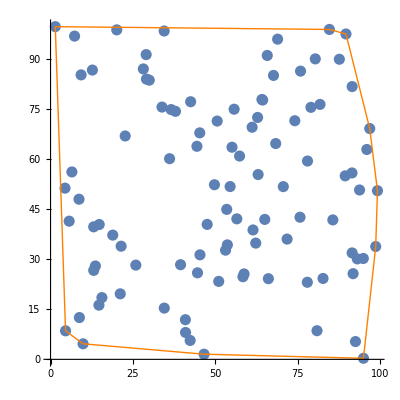

```mathematica
Show[ListPlot[vertices, PlotStyle-> {PointSize[.02]}], Boundary[ch,{Thick, Orange}], AspectRatio-> 1]
```